# Ashcroft and Mermin Chapter 1

## Question 4 - Helical Waves

### Part a) Solve Diff Eqn

- Dynamic solution

```mathematica
Solve[{D[Px,t]== -e Ex ⅇ^(-ⅈ ω t)-ωc Py - Px/τ,D[Py,t]==-e Ey ⅇ^(-ⅈ ω t)+ωc Px - Px/τ},{Px, Py}]
```

{{Px→(e ⅇ^(-ⅈ t ω) Ey τ)/(-1+τ ωc),Py→-(e ⅇ^(-ⅈ t ω) (-Ex+Ey+Ex τ ωc))/(ωc (-1+τ ωc))}}

- Steady state solution

```mathematica
Solve[{-ⅈ ω Px== -e Ex-ωc Py - Px/τ,-ⅈ ω Py== -e Ey+ωc Px - Px/τ},{Px, Py}]
```

{{Px→-(τ (ⅈ e Ex ω+e Ey ωc))/(ⅈ ω+τ ω^2+ωc-τ ωc^2),Py→-(-e Ex+e Ey-ⅈ e Ey τ ω+e Ex τ ωc)/(-ⅈ ω-τ ω^2-ωc+τ ωc^2)}}

### Part c) Plots

In CGS:

```mathematica
e=4.80320427×10^-10;
Subscript[m, e]=9.1094×10^-28;
c = 2.99792458×10^10;
```

```mathematica
(*
ωp=(4π n  e^2)/Subscript[m, e];
ωc=(e H)/(Subscript[m, e] c);
*)
```

```mathematica
ϵ0m[ω_]:=1-ωp/ω(1/(ω-ωc+ⅈ/τ));
ϵ0p[ω_]:=1-ωp/ω(1/(ω+ωc+ⅈ/τ));
```

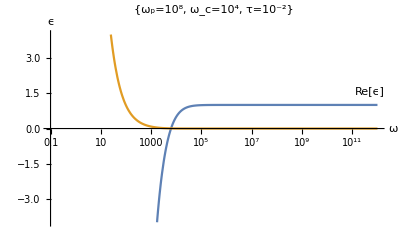

```mathematica
plots1={Re[ϵ0p[ω]],Im[ϵ0p[ω]]}/.{ωp-> 10^8, ωc-> 10^4,τ->10^-2 };
LogLinearPlot[{plots1⟦1⟧,plots1⟦2⟧},{ω,10^-1,10^12},PlotLabels->Placed[{"Re[ϵ]","Im[ϵ]"},Above],AxesLabel->{"ω","ϵ"},PlotLabel->{"ω_p=10^8, ω_c=10^4, τ=10^-2"}]
```

### Part d) Estimation

```mathematica
ωp[n_]:=√((4π n  e^2)/Subscript[m, e]);
ωc[H_]:=(e H)/(Subscript[m, e] c);
```

```mathematica
ωH=ωc[H]((k^2 c^2)/ωp[n]^2);
fH =  ωH/2π;
```

```mathematica
{c,e,Subscript[m, e]}
```

{2.99792×10^10,4.8032×10^-10,9.1094×10^-28}

```mathematica
fH
```

(c H k^2)/(8 e n)

```mathematica
fH/.{n-> 10^22,H-> 10^4,k-> (2π)/1}
```

308.006

## Question 5 - Plasmons

### Part B) Plot

```mathematica
σ0=(n e^2)/Subscript[m, e]
σ[ω_]:= σ0 1/(1-ⅈ ω τ);
ϵ[ω_]:=1 + (4π σ[ω])/ω ⅈ; 

qc2 [ω_]:= ω^2(1-ω^2/(2 ω^2-ωp^2));
```

(e^2 n)/m_e

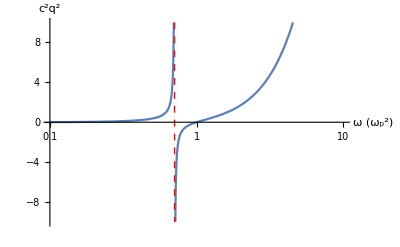

```mathematica
LogLinearPlot[qc2[ω]/.{ωp-> 1},{ω,10^-1,10},
AxesLabel->{"ω (ω_p^2)","c^2q^2"},
PlotRange->{-10,10},
Exclusions->{2 ω^2-1== 0}, ExclusionsStyle->{Directive[Red,Dashed]}]
```